### Airfoil Specifications: A18

#### Aerodynamic Data

```mathematica
A18AlphaData=List[-9.5,-9.25,-9.0,-8.75,-8.5,-8.25,-8.0,-7.75,-7.5,-7.25,-7.0,-6.75,-6.5,-6.25,-6.0,-5.75,-5.5,-5.25,-5.0,-4.75,-4.5,-4.25,-4.0,-3.75,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-2.0,-1.75,-1.5,-1.25,-1.0,-0.75,-0.5,-0.25,0.0,0.25,0.5,0.75,1.0,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.0,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25,12.5];
A18CLData=List[-0.4443,-0.4551,-0.4655,-0.4733,-0.4792,-0.4593,-0.431,-0.4061,-0.3775,-0.3422,-0.307,-0.2723,-0.2369,-0.2006,-0.1662,-0.1313,-0.0951,-0.0624,-0.0272,0.0096,0.0415,0.0754,0.1105,0.1409,0.1742,0.2073,0.2383,0.2721,0.3022,0.334,0.365,0.395,0.4255,0.4552,0.4838,0.5113,0.5352,0.5594,0.5876,0.615,0.6424,0.6695,0.6965,0.7235,0.7503,0.7769,0.8032,0.8295,0.8553,0.881,0.9061,0.9306,0.9524,0.9755,0.9928,1.0127,1.0353,1.0573,1.0767,1.0964,1.1174,1.1387,1.1585,1.1746,1.1923,1.2095,1.2269,1.2443,1.2608,1.2761,1.2905,1.3036,1.3151,1.3252,1.3333,1.3375,1.3364,1.3326,1.3263,1.3179,1.3064,1.2937,1.2783,1.2608,1.2421,1.2217,1.2003,1.1776,1.154];
A18CDData=List[0.086,0.08249,0.07857,0.07371,0.06745,0.02683,0.02267,0.02145,0.02003,0.01853,0.01806,0.01798,0.01752,0.01752,0.01749,0.01659,0.01593,0.01542,0.01483,0.01429,0.01368,0.01323,0.01285,0.01257,0.01222,0.01194,0.01166,0.01138,0.01115,0.01091,0.01074,0.01055,0.01032,0.01014,0.00984,0.00951,0.00905,0.00868,0.00876,0.00887,0.009,0.00914,0.00931,0.00949,0.00967,0.00988,0.0101,0.01034,0.01062,0.01092,0.01127,0.01165,0.01225,0.01282,0.01405,0.01509,0.01578,0.01652,0.01761,0.01869,0.0196,0.02042,0.02142,0.02285,0.02402,0.02525,0.02649,0.02768,0.02898,0.03054,0.03232,0.03452,0.03746,0.04029,0.04266,0.04499,0.04725,0.04975,0.05252,0.05553,0.0591,0.06296,0.06751,0.07275,0.07869,0.08555,0.09339,0.10243,0.11286];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
A18FCL = Interpolation[Thread[{A18AlphaData, A18CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
A18FCD= Interpolation[Thread[{A18AlphaData, A18CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[A18FCL[α],"CL"], Labeled[A18FCD[α],"CD"]},{α, -9.5, 12.5}, AxesLabel->{"Angel α","Coefficient"}]]
```

-Graphics-

#### Airfoil Geometry

```mathematica
A18Geometry = List[{1.00000000,0.00614000},{0.94999999,0.01817000},{0.89999998,0.02858000},{0.80000001,0.04624000},{0.69999999,0.06056000},{0.60000002,0.07197000},{0.55000001,0.07612000},{0.50000000,0.07975000},{0.44999999,0.08293000},{0.40000001,0.08376000},{0.34999999,0.08466000},{0.30000001,0.08383000},{0.25000000,0.08065000},{0.20000000,0.07601000},{0.15000001,0.07026000},{0.10000000,0.06234000},{0.07500000,0.05660000},{0.05000000,0.04923000},{0.02500000,0.03947000},{0.01250000,0.03239000},{0.00000000,0.01865000},{0.01250000,0.00781000},{0.02500000,0.00357000},{0.05000000,0.00075000},{0.07500000,0.00000000},{0.10000000,0.00006000},{0.15000001,0.00200000},{0.20000000,0.00475000},{0.25000000,0.00806000},{0.30000001,0.01038000},{0.34999999,0.01353000},{0.40000001,0.01657000},{0.44999999,0.01780000},{0.50000000,0.01884000},{0.55000001,0.01980000},{0.60000002,0.01998000},{0.69999999,0.01924000},{0.80000001,0.01452000},{0.89999998,0.00813000},{0.94999999,0.00434000},{1.00000000,0.00000000}];
```

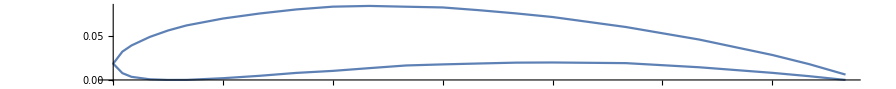

```mathematica
ListLinePlot[A18Geometry, AspectRatio->.1]
```